To do: fix the generation of ticks for logarithmic scale in the function LatexPlot.

# LatexPlot`Usage

## Given a plot, LATEX it!

For criticism, suggestions and requests: lissadesouzacampos@gmail.com

I really like Mathematica default style, but when writing papers, I need compatible LATEX like plots with a black frame and right fonts.. The LatexPlot package have one main function LatexPlot[] which receives a plot and make it LATEX style!

```mathematica
Import["C:\\Users\\Lissa\\Google Drive\\Wolfram Mathematica\\MyPackages\\LatexPlot.m"]
```

## myPalette.

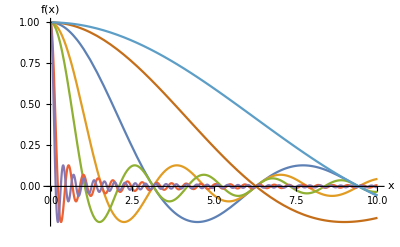

```mathematica
example0=Plot[{
Sinc[x],Sinc[2 x],Sinc[3 x],Sinc[14x],Sinc[20x],Sinc[1/2 x],Sinc[1/3 x]},{x,0,10},AxesLabel->{"x","f(x)"},PlotTheme->"Default"]
```

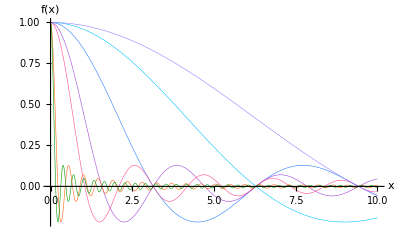

```mathematica
example1=Plot[{
Sinc[x],Sinc[2 x],Sinc[3 x],Sinc[14x],Sinc[20x],Sinc[1/2 x],Sinc[1/3 x]},{x,0,10},AxesLabel->{"x","f(x)"},PlotTheme->"myPalette"]
```

## ReStylePlot.

This is an auxiliary function to LatexPlot. It simply takes the data of the plot and re-plot it with new styling options. It needs to know if your giving it a line plot or a list plot, the user specifies that in the second argument.

For a ListLinePlot:

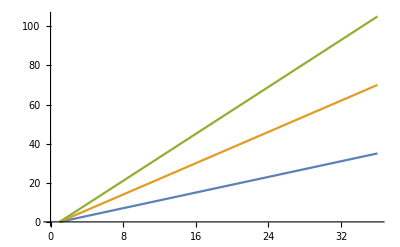

```mathematica
example2=ListLinePlot[{Table[x,{x,0,35}],Table[2x,{x,0,35}],Table[3x,{x,0,35}]}]
```

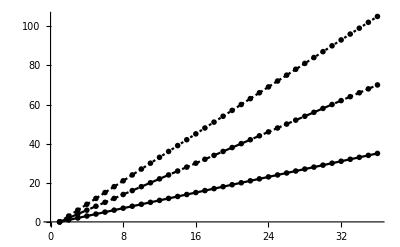

```mathematica
example3=ReStylePlot[example2,Line,PlotTheme->"Monochrome"]
```

For a ListPlot or, in particular, a ListLogPlot, one has to specify that is not a Line:

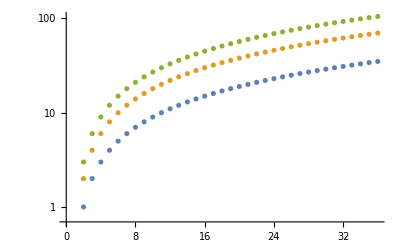

```mathematica
example4=ListLogPlot[{Table[x,{x,0,35}],Table[2x,{x,0,35}],Table[3x,{x,0,35}]}]
```

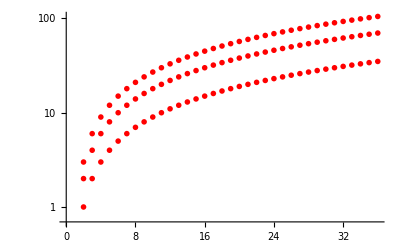

```mathematica
example5=ReStylePlot[example4,List,PlotStyle->Red,PlotMarkers-> ♡]
```

A default Plot is a LinePlot:

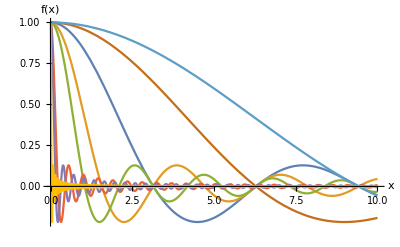

```mathematica
example0=Plot[{
Sinc[x],Sinc[2 x],Sinc[3 x],Sinc[14x],Sinc[20x],Sinc[1/2 x],Sinc[1/3 x],Sinc[100 x]},{x,0,10},AxesLabel->{"x","f(x)"},PlotTheme->"Default"]
```

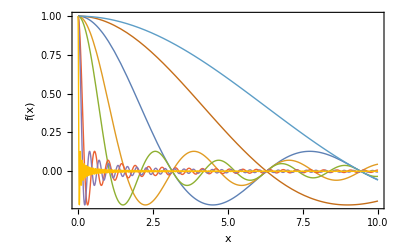

```mathematica
example6=ReStylePlot[example0,Line,PlotStyle->Thick,Frame->True]
```

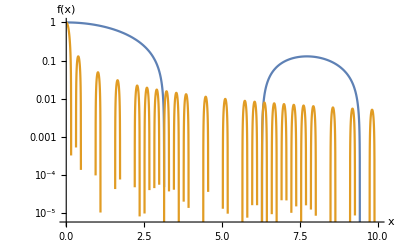

```mathematica
example0Log=LogPlot[{
Sinc[x],Sinc[20x]},{x,0,10},AxesLabel->{"x","f(x)"},PlotTheme->"Default"]
```

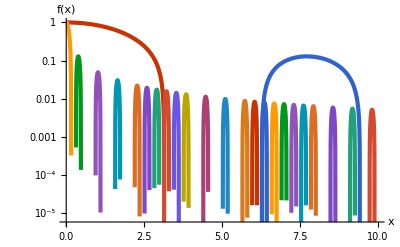

```mathematica
example7=ReStylePlot[example0Log,Line,PlotTheme->"Web"]
```

Last one just to check “myPalette” again:

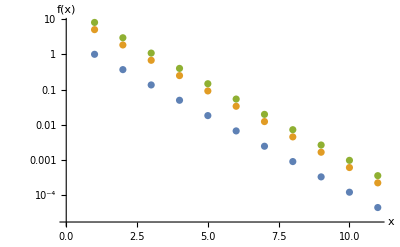

```mathematica
example8=ListLogPlot[{Table[ⅇ^-x,{x,0,10}],Table[5 ⅇ^-x,{x,0,10}],Table[8 ⅇ^-x,{x,0,10}]},AxesLabel->{"x","f(x)"},PlotTheme->"Default"]
```

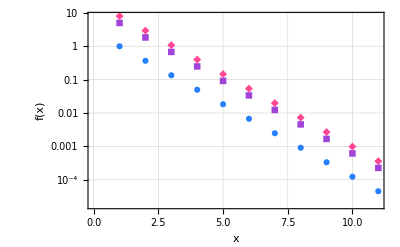

```mathematica
example9=ReStylePlot[example8,List,PlotTheme->"myPalette",PlotMarkers->Automatic,GridLines->Automatic,GridLinesStyle->{LightGray,Dashed}, Frame->True]
```

## Main function: LatexPlot.

Some options of LatexPlot work just as those of a normal Plot. The ones that start with lower case are options defined for this particular function by me.

```mathematica
LatexPlot//Options
```

{FontSize→20,Thickness→Large,closedFrame→True,minorTicks→False,majorTicks→True,Rotate→False,ImageSize→500,leftTicks→False,bottomTicks→False,GridLines→Automatic,GridLinesStyle→Directive[{GrayLevel[0.5],Dashing[{Small,Small}],Thickness[Small]}],AxesLabel→False,PlotStyle→None,PlotTheme→myPalette,PlotRange→Automatic,listPlot→False,logPlot→False,ticks→True}

```mathematica
example0=Plot[{
Sinc[x],Sinc[2 x],Sinc[3 x],Sinc[14x],Sinc[20x],Sinc[1/2 x],Sinc[1/3 x]},{x,0,10},AxesLabel->{"x","f(x)"},PlotTheme->"Default"]
```

-Graphics-

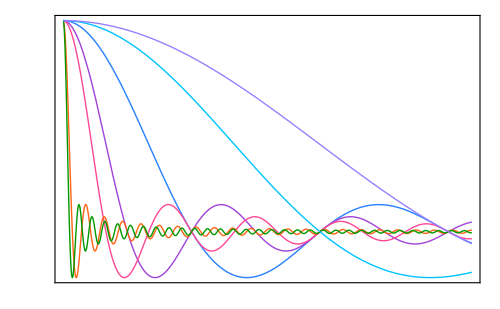

```mathematica
example11=LatexPlot[example0]
```

Do note that if you export this as pdf it will not actually look like the above plot. It will look like a Rasterized version of it :

```mathematica
example11inaPDF=Rasterize[LatexPlot[example0],ImageResolution->500]
```

-Graphics-

Moreover, since LatexPlot adds a Frame and generates ticks with LATEX style, the settings of the Axes or Frames or the original plot are thrown away.  The user can choose many things though, let’s see some examples.

Options that work as those of a normal plot:  FontSize, Thickness, Rotate, ImageSize, GridLines, GridLinesStyle, AxesLabel, PlotStyle, PlotTheme, PlotRange

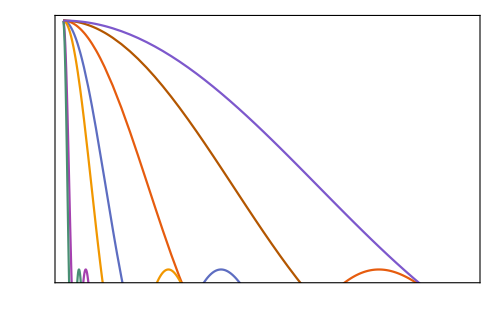

```mathematica
example12=LatexPlot[example0,FontSize->20,Thickness->0.001,Rotate->False,GridLines->None,PlotRange->{0.1,1},PlotTheme->"Scientific"]
```

"New" Options: closedFrame, minorTicks, majorTicks, leftTicks, bottomTicks, listPlot, logPlot, ticks.

```mathematica
example13=LatexPlot[example0,"closedFrame"->False,"minorTicks" ->True,"leftTicks"->{0.5}]
```

-Graphics-

If the plot given as argument was given a ListPlot, one has to specify it using the option “listPlot”, because of the function ReStylePlot.

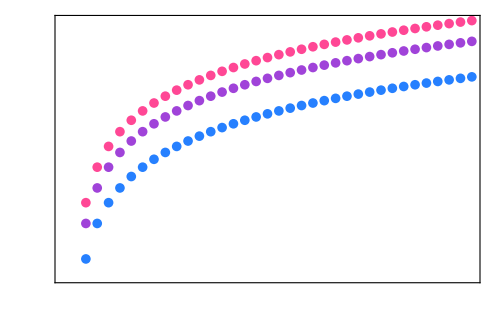

```mathematica
example14=LatexPlot[example4, "listPlot"->True]
```

The option logPlot toggle the generation of the ticks from linear to logarithmic. This feature DOES NOT work properly. If the numbers are reasonable, it can look bad:

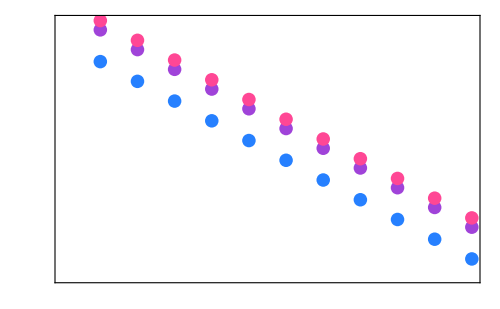

```mathematica
example15=LatexPlot[example8,"listPlot"->True,"logPlot"->True]
```

But if the numbers are super small, like 10^-300 , then it becomes unreadable. And it can take up to 200 seconds to generate it!

## AddLegend.

If the plot also has legends to be MaTeXed, please specify that. Let’s see some examples of that.

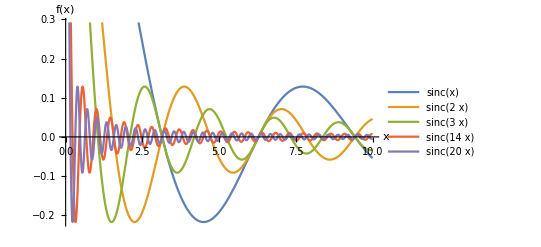

```mathematica
example0=Plot[{
Sinc[x],Sinc[2 x],Sinc[3 x],Sinc[14x],Sinc[20x]},{x,0,10},AxesLabel->{"x","f(x)"},PlotLegends->"Expressions"]
```

If your plot has legends,  like example0 above, then both ReStylePlot and LatexPlot will not be well defined for example0, but will work normally for example0[[1]].

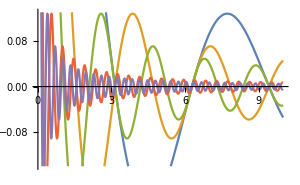
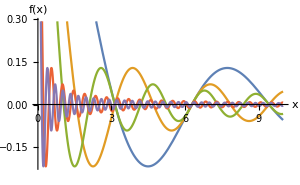

```mathematica
{Show[ReStylePlot[example0],ImageSize->300], Show[ReStylePlot[example0[[1]]],ImageSize->300]}
```

The first part is just the plot without the legends, and the [[2,1,2]] part gives us the automatically generated legends:

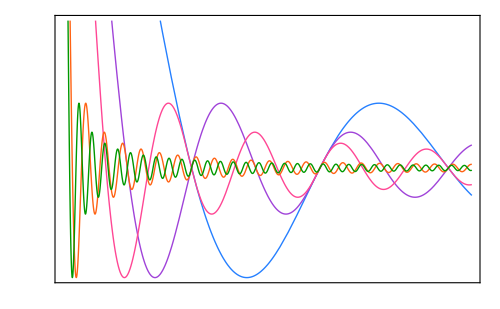
{-Graphics-,{Sinc[x],Sinc[2 x],Sinc[3 x],Sinc[14 x],Sinc[20 x]}}

```mathematica
{LatexPlot[example0[[1]]],example0[[2,1,2]]}
```

To add MaTeXed legends with the same colors of “myPalette”, use the function AddLegend:

```mathematica
example16=AddLegends[LatexPlot[example0[[1]]],example0[[2,1,2]]]
```

-Graphics-

But one can add any legend. If it does NOT need to be MaTeXed, then one has to specify, for example:

```mathematica
example17=AddLegends[LatexPlot[example0[[1]]],{"These","are","not","math","stuff"},"text"->True]
```

-Graphics-

In a pdf, the legends would look thicker:

```mathematica
example18=Rasterize[AddLegends[LatexPlot[example0[[1]]],Range[5]],ImageResolution->500]
```

-Graphics-

If you have a lot of curves:

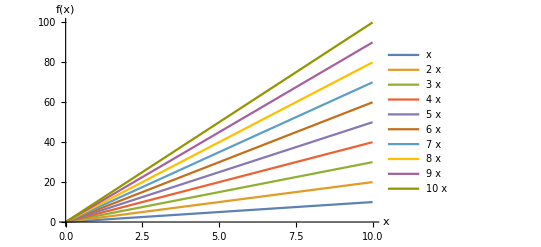

```mathematica
example19=Plot[{x,2x,3x,4x,5x,6x,7x,8x,9x,10x},{x,0,10},AxesLabel->{"x","f(x)"},PlotLegends->"Expressions"]
```

Then you might want to add legends in more than 1 column:

```mathematica
example20 = Rasterize[AddLegends[LatexPlot[example19[[1]]], example19[[2,1,2]] ,"columns"->2],ImageResolution->500]
```

-Graphics-

Since otherwise it looks bad:

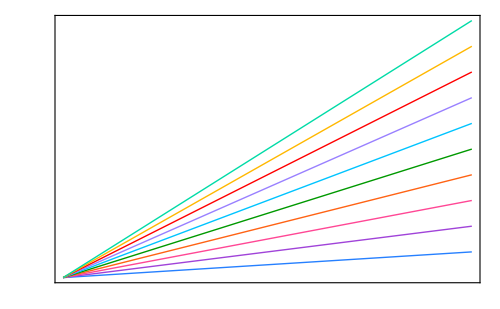

```mathematica
AddLegends[LatexPlot[example19[[1]]], example19[[2,1,2]] ]
```

## Comments.

There has got to be a better way of LaTeXifying a plot. For example, this solution to make a plot look like xkcd:

```mathematica
Hyperlink["https://mathematica.stackexchange.com/questions/11350/xkcd-style-plots"]
```

https://mathematica.stackexchange.com/questions/11350/xkcd-style-plots

is AWESOME! and super fun! But I am still learning the language and this solution was good enough for my first paper.

Problem: I couldn’t add arrow to a Frame, only to Axes. But when I LATEX a plot, I use Frame because of the Ticks that I want to be in LATEX form. So I couldn’t implement the y-x axes with arrows style to the LatexPlot function. The PlotTheme “myArrows” was the best I could in this respect; but is very low resolution fugly arrows.

```mathematica
Themes`AddThemeRules["myArrows", 
DefaultPlotStyle->Thread@Directive[{RGBColor[0.12, 0.42, 1.],RGBColor[0, 0.6, 0],RGBColor[1., 0.39, 0.08],Hue[0.77, 1., 0.98],Hue[0.46, 1, 0.86],Hue[0.9],Hue[1.12],RGBColor[0.11, 0.59, 1],Hue[Rational[5, 6], 1, Rational[1, 2]],Hue[0.47000000000000003, 0.77, 0.63],Hue[0, 1, 1] ,Hue[0.7, 0.5]},Thickness[0.001]],
AxesStyle->Directive[ Black,Arrowheads[{{Automatic,Automatic, Graphics[Line[{{{-2/3,1/4},{0,0},{-2/3,-1/4}}}]]     }}]],
LabelStyle->{FontFamily->"Latin Modern Math",FontSize->14,  Black},
ImageSize-> 500
];
```

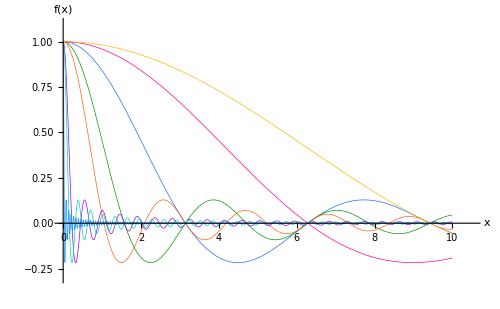

```mathematica
example21=Plot[{
Sinc[x],Sinc[2 x],Sinc[3 x],Sinc[14x],Sinc[20x],Sinc[1/2 x],Sinc[1/3 x],Sinc[100 x]},{x,0,10},PlotRange->{ {0,10.5},{-0.3,1.1}} ,AxesLabel->{"x","f(x)"}, PlotTheme->"myArrows"]
```

But the function ReStylePlot is not compatible with those arrowheads! But the arrows look so bad I didn’t think it was worth making ReStylePlot compatible with it anyway.

```mathematica
example22=ReStylePlot[example21 ]
```

ListLinePlot::lpn: {{{2.04082×10^-7,1.},{0.00306718,0.999998},{0.00613415,0.999994},{0.00920113,0.999986},{0.0122681,0.999975},{0.0153351,0.999961},{0.0184021,0.999944},{0.021469,0.999923},{0.024536,0.9999},{0.027603,0.999873},{0.03067,0.999843},{0.0337369,0.99981},«27»,{0.199612,0.993372},{0.202937,0.99315},{0.209586,0.992695},{0.222886,0.991741},{0.249486,0.989658},{0.252811,0.989382},{0.256136,0.989102},{0.262786,0.98853},{0.276085,0.987344},{0.302685,0.9848},{0.30601,0.984466},«433»},«7»,{}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{{2.04082×10^-7,1.},{0.00306718,0.999998},{0.00613415,0.999994},{0.00920113,0.999986},{0.0122681,0.999975},{0.0153351,0.999961},{0.0184021,0.999944},{0.021469,0.999923},{0.024536,0.9999},{0.027603,0.999873},{0.03067,0.999843},461,{9.94852,-0.050271},{9.95195,-0.050552},{9.95881,-0.0511117},{9.97254,-0.0522214},{9.97597,-0.0524968},{9.97941,-0.0527715},{9.98627,-0.0533183},{9.9897,-0.0535905},{9.99314,-0.0538618},{9.99657,-0.0541324},{10.,-0.0544021}},7,{{1}}},1]
 |  |  |  |